```mathematica
(*zad1*)
x = Random[Integer, {0, 20}]
y = Random[Real, {-100, 100}]
PrimeQ[x]
y > 0
```

8

18.2011

False

True

```mathematica
(*zad2*)
= - przypisanie zmiennej, wartości funkcji itp. do zmiennej,
== - porównanie ze sobą np. wyników operacji matematycznej, wartości zmiennych itp.
=== - tożsamość, porównanie czy dwa obiekty wskazują na to samo miejsce w pamięci
```

```mathematica
(*zad3*)
```

```mathematica
f[n_]:=f[n]=f[n-1]+f[n-2];
f[1]=1;f[2]=1;
ft = Array[f, 10]

f2[n_]:=f2[n-1]^2;
f2[1]=3;
Array[f2, 5]
```

{1,1,2,3,5,8,13,21,34,55}

{3,81,6561,43046721,1853020188851841}

```mathematica
(*zad4*)
= - wartość funkcji jest obliczana przy de.1cniowaniu funkcj
=: - wartość funkcji jest obliczana przy wywołaniu funkcji dla argumentu
```

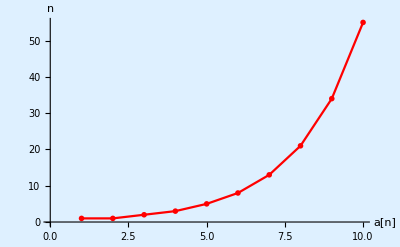

```mathematica
(*zad5*)
ListPlot[ft, AxesLabel->{"a[n]", "n"}, Background->LightBlue, PlotStyle->Red, PlotMarkers->GoldenRatio, Joined->True]
```

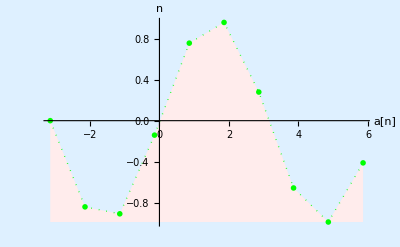

```mathematica
(*zad6*)
ListPlot[Table[{x, Sin[x]}, {x,-Pi, 2*Pi}], AxesLabel->{"a[n]", "n"}, Background->LightBlue, PlotStyle->{Thick, Green, Dotted}, PlotMarkers->GoldenRatio, Joined->True, Filling->Bottom, FillingStyle->LightPink]
```

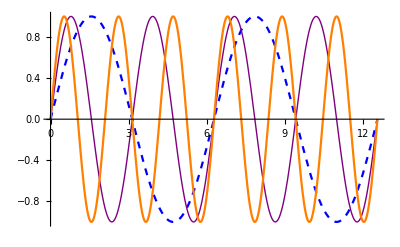

```mathematica
(*zad7*)
f1 = Plot[Sin[x], {x,0, 4*Pi},  PlotStyle->{Blue, Dashed}];
f2 = Plot[Sin[2*x], {x,0, 4*Pi},  PlotStyle->{Purple, Thick}];
f3=Plot[Sin[3*x], {x,0, 4*Pi},  PlotStyle->{Orange}];
Show[f1,f2,f3]
```

```mathematica
(*zad8*)
Plot3D[Sin[x^2+y^2],{x,-Pi,Pi},{y,-Pi,Pi},PlotStyle->{Green},Axes->False,Mesh->None]
```

-Graphics3D-

```mathematica
(*zad9*)
ParametricPlot3D[{Cos[t]*(3+Cos[u]),Sin[t]*(3+Cos[u]),Sin[u]},{t,0,2*Pi},{u,0,2*Pi}]
```

-Graphics3D-

```mathematica
(*zad10*)
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,0,4},AnimationRunning->False]
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,0,8,2},AnimationRunning->False]
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,{0,4,7,8}},AnimationRunning->False]
(*bez AnimationRunning->False zawiesza Mathematicę*)
```

```mathematica
(*zad11*)
Animate[Plot3D[E^(a*Sin[x+y]+b*Cos[x-y]),{x,0,2*π},{y,0,2*π},PlotRange->{0,9}],{a,0,1},{b,0,9,2},AnimationRunning->False]
```